```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\ethans\Overleaf\MATH162\Notes\img

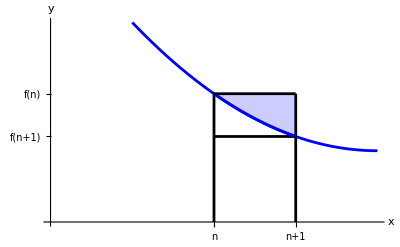

series_integral_diff.png

```mathematica
f[t_]=(t-4)^2+5;
{a,b}={1,4};
n=2;
plt=Show[
Plot[f[t],{t,a,b},AxesOrigin->{0,0},PlotStyle->Blue],
Plot[{f[t],f[n],f[n+1]},{t,n,n+1},Filling->{1->{2}},PlotStyle->{Blue,Black,Black}],
ContourPlot[{x==n,x==n+1},{x,a,b},{y,0,f[n]},ContourStyle->Black],
Ticks->{{{n,"n"},{n+1,"n+1"}},{{f[n],"f(n)"}, {f[n+1], "f(n+1)"}}},
AxesLabel->{x,y}
]
Export["series_integral_diff.png",plt]
```

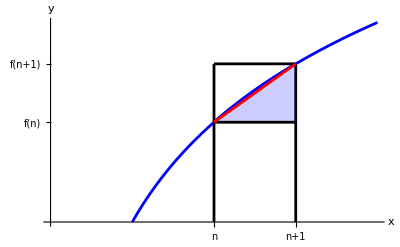

```mathematica
f[t_]=Log[t];
n=2;
{a,b}={n-1,n+2};
l[t_]=Log[n]+(Log[n+1]-Log[n])*(t-n);
plt=Show[
Plot[f[t],{t,a,b},AxesOrigin->{0,0},PlotStyle->Blue],
Plot[{f[t],f[n],f[n+1],l[t]},{t,n,n+1},Filling->{1->{2}},PlotStyle->{Blue,Black,Black,Red}],
ContourPlot[{x==n,x==n+1},{x,a,b},{y,0,f[n+1]},ContourStyle->Black,PlotRange->{0,f[b]}],
Ticks->{{{n,"n"},{n+1,"n+1"}},{{f[n],"f(n)"}, {f[n+1], "f(n+1)"}}},
AxesLabel->{x,y},
AxesOrigin->{0,0}
]
```